# Symmetric perceptron, Rectangular Activation

## First Moment Upper Bound

```mathematica
A[y_,qh_]:=Log[Sum[Exp[(y-2k)^2 qh/2] Binomial[y,k],{k,0,y}]]
```

```mathematica
S[y_,qh_,q_]:=-qh y/2 - q qh y (y-1)/2+A[y,qh]
```

```mathematica
DS[y_,qh_,q_]:=-y/2-1/2 q (-1+y) y+(∑_(k=0)^y (2 ⅇ^(1/2 qh (-2 k+y)^2) k^2-2 ⅇ^(1/2 qh (-2 k+y)^2) k y+1/2 ⅇ^(1/2 qh (-2 k+y)^2) y^2) Binomial[y,k])/(∑_(k=0)^y ⅇ^(1/2 qh (-2 k+y)^2) Binomial[y,k])
```

```mathematica
G[y_,q_]:=Module[{qh},
qh=FindRoot[DS[y,z,q],{z,0}][[1,2]];
S[y,qh,q]
]
```

```mathematica
g[z_]:=Exp[-z^2/2]/Sqrt[2π]
H[z_]:=1/2Erfc[z/Sqrt[2]]
```

```mathematica
GE[y_,q_]:=Log[NIntegrate[g[z]H[-Sqrt[q]z/Sqrt[1-q]]^y,{z,-∞,∞}]]
```

```mathematica
GEs[y_,q_,k_]:=Log[NIntegrate[g[z](H[-k/Sqrt[1-q]+Sqrt[q]z/Sqrt[1-q]]-H[k/Sqrt[1-q]+Sqrt[q]z/Sqrt[1-q]])^y,{z,-∞,∞}]]
```

```mathematica
phi[y_,q_,α_]:=G[y,q]+α GE[y,q]
```

```mathematica
phis[y_,q_,α_,k_]:=G[y,q]+α GEs[y,q,k]
```

```mathematica
alpha[y_,q_]:=-G[y,q]/GE[y,q]
```

```mathematica
alphas[y_,q_,k_]:=-G[y,q]/GEs[y,q, k]
```

```mathematica
alphasRC[k_]:= -Log[2]/Log[Erf[k/Sqrt[2]]]
```

Follow little comparison with Julia program to check that the code in Julia is correct:

```mathematica
2*phis[2,0.99,0.1,1]
```

1.36475

Check seemes OK!

### RIGOROUS: First Moment Upper Bound, y=2, K=1.

```mathematica
qrect[ β_,K_]:=1/(2π)NIntegrate[NIntegrate[ⅇ^(-(x^2+y^2)/2),{x,(-K+(1-2β)y)/(2√(β(1-β))),(K+(1-2β)y)/(2√(β(1-β)))}],{y,-K,K}]
```

```mathematica
qrectSmart[ β_,K_]:=NIntegrate[(ⅇ^(-y^2/2))/(√(2π))(1/2 Erfc[(-K+(1-2β)y)/(2 √2 √(β(1-β)))]-1/2 Erfc[(K+(1-2β)y)/(2 √2 √(β(1-β)))]),
					{y,-K,K}]
```

```mathematica
alphasRigorous[β_]:= -(Log[2]-β Log[β]-(1-β)Log[1-β])/Log[qrectSmart[ β,1]]
```

```mathematica
With[{x=0.01},qrectSmart[ 1-x,1.]]
```

0.644077

I write the part below just to export the calculation of the first moment and plot the upper bound in Julia. Need it for comparison with lower bound.

```mathematica
UBlist=N[Join[Table[{x, alphasRigorous[1-x]},{x,10^-3,9*10^-3,10^-3}],
Table[{x, alphasRigorous[1-x]},{x,10^-2,9*10^-2,10^-2}],
Table[{x, alphasRigorous[1-x]},{x,0.1,0.5,0.05}]]]
```

{{0.001,1.75368},{0.002,1.73708},{0.003,1.727},{0.004,1.72005},{0.005,1.71497},{0.006,1.71114},{0.007,1.7082},{0.008,1.70593},{0.009,1.70419},{0.01,1.70285},{0.02,1.70118},{0.03,1.70765},{0.04,1.71618},{0.05,1.72498},{0.06,1.73341},{0.07,1.7412},{0.08,1.74826},{0.09,1.7546},{0.1,1.76026},{0.15,1.78058},{0.2,1.79269},{0.25,1.80072},{0.3,1.80647},{0.35,1.81066},{0.4,1.81357},{0.45,1.8153},{0.5,1.81588}}

```mathematica
Export["UBtable.txt",UBlist,"Table"]
```

UBtable.txt

```mathematica
Directory[]
```

/Users/riccardodellavecchia

Check with program in Julia that does the rigorous lower bound.

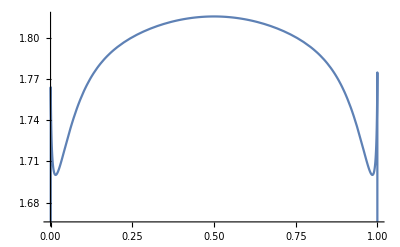

```mathematica
Plot[alphasRigorous[β],{β,0,1}]
```

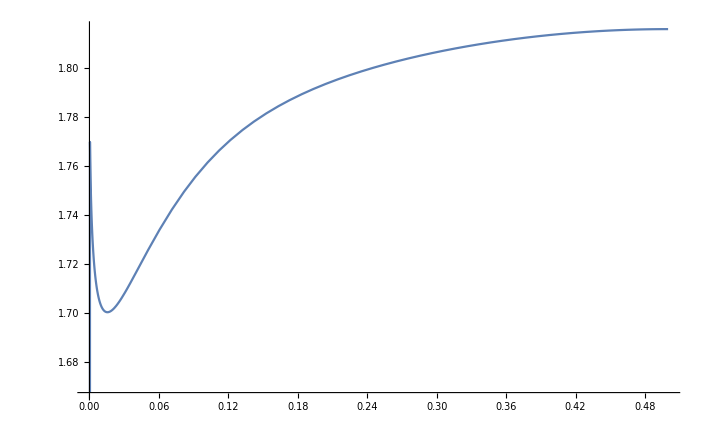

```mathematica
Plot[{alphasRigorous[β],alphas[2,1-2β,1]},{β,0,0.5}]
```

Done with replicas or rigorously the two solutions conincide!

```mathematica
Table[{β, N[alphasRigorous[β]]},{β,0.01,0.5,0.02}]
```

{{0.01,1.70285},{0.03,1.70765},{0.05,1.72498},{0.07,1.7412},{0.09,1.7546},{0.11,1.7653},{0.13,1.77379},{0.15,1.78058},{0.17,1.78611},{0.19,1.79068},{0.21,1.79454},{0.23,1.79785},{0.25,1.80072},{0.27,1.80324},{0.29,1.80546},{0.31,1.80742},{0.33,1.80915},{0.35,1.81066},{0.37,1.81197},{0.39,1.81309},{0.41,1.81401},{0.43,1.81475},{0.45,1.8153},{0.47,1.81567},{0.49,1.81585}}

```mathematica
Table[{β,alphas[2,1-2β,1]},{β,0.01,0.5,0.02}]
```

{{0.01,1.70285},{0.03,1.70765},{0.05,1.72498},{0.07,1.7412},{0.09,1.7546},{0.11,1.7653},{0.13,1.77379},{0.15,1.78058},{0.17,1.78611},{0.19,1.79068},{0.21,1.79454},{0.23,1.79785},{0.25,1.80072},{0.27,1.80324},{0.29,1.80546},{0.31,1.80742},{0.33,1.80915},{0.35,1.81066},{0.37,1.81197},{0.39,1.81309},{0.41,1.81401},{0.43,1.81475},{0.45,1.8153},{0.47,1.81567},{0.49,1.81585}}

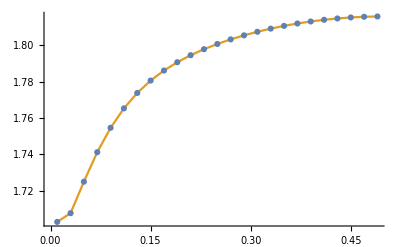

```mathematica
ListPlot[{%344,%330},Joined->{False, True}]
```

Just another check that the two ways give same results.

### K=2

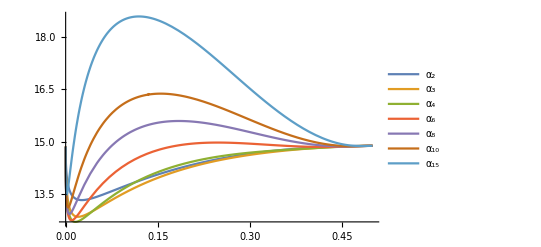

```mathematica
Plot[{alphas[2,1-2x,2],alphas[3,1-2x,2],alphas[4,1-2x,2],alphas[6,1-2x,2],alphas[8,1-2x,2],alphas[10,1-2x,2],alphas[15,1-2x,2]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10","α_15"}, PlotRange->All]
```

### K=1

```mathematica
N[alphasRC[1]]
```

1.81588

```mathematica
alphas[2,0.98,1]
```

1.70285

```mathematica
With[{x= 0.001},alphas[2,1-2x,1.]]
```

1.75368

UBs (1.759 ...,n=100)

```mathematica
alphas[2,0.98,1.]
```

0.212713

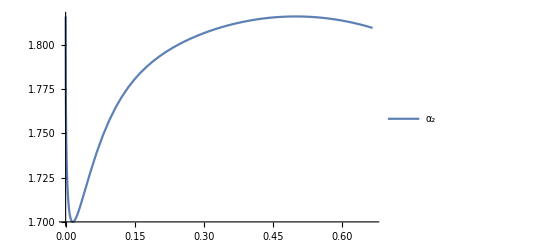

```mathematica
Plot[{alphas[2,1-2x,1]},{x,0,2/3}, PlotLegends->{"α_2"}]
```

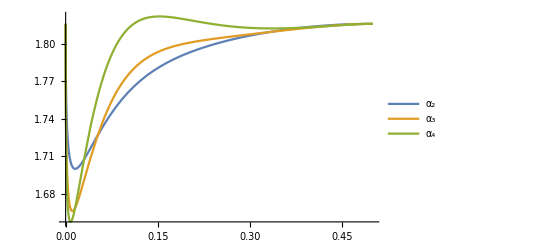

```mathematica
Plot[{alphas[2,1-2x,1],alphas[3,1-2x,1],alphas[4,1-2x,1]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4"}]
```

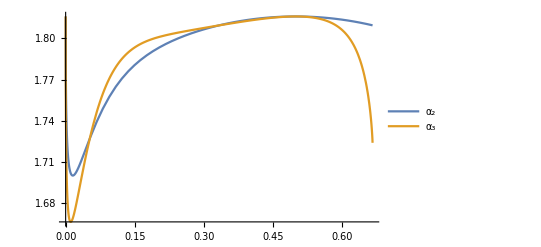

```mathematica
Plot[{alphas[2,1-2x,1],alphas[3,1-2x,1]},{x,0,2/3}, PlotLegends->{"α_2","α_3"}]
```

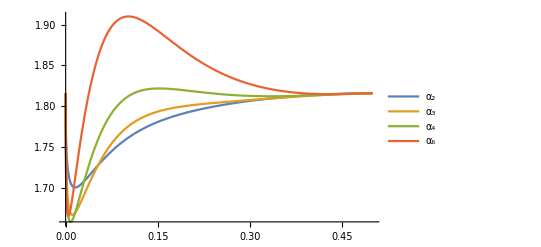

```mathematica
Plot[{alphas[2,1-2x,1],alphas[3,1-2x,1],alphas[4,1-2x,1],alphas[6,1-2x,1]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6"}, PlotRange->All]
```

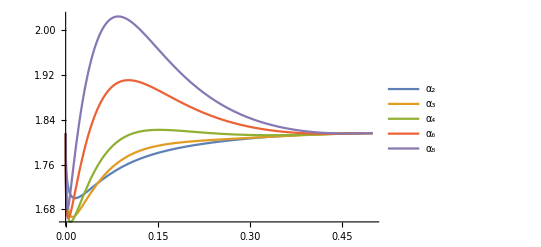

```mathematica
Plot[{alphas[2,1-2x,1],alphas[3,1-2x,1],alphas[4,1-2x,1],alphas[6,1-2x,1],alphas[8,1-2x,1]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8"}, PlotRange->All]
```

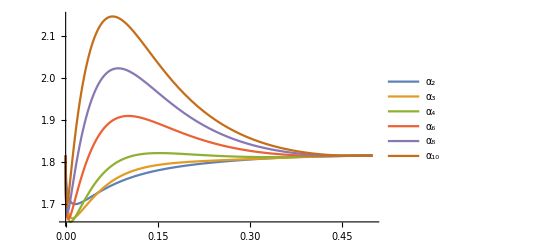

```mathematica
Plot[{alphas[2,1-2x,1],alphas[3,1-2x,1],alphas[4,1-2x,1],alphas[6,1-2x,1],alphas[8,1-2x,1],alphas[10,1-2x,1]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10"}, PlotRange->All]
```

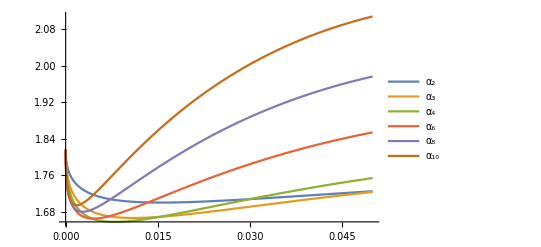

```mathematica
Plot[{alphas[2,1-2x,1],alphas[3,1-2x,1],alphas[4,1-2x,1],alphas[6,1-2x,1],alphas[8,1-2x,1],alphas[10,1-2x,1]},{x,0,0.05}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10"}, PlotRange->All]
```

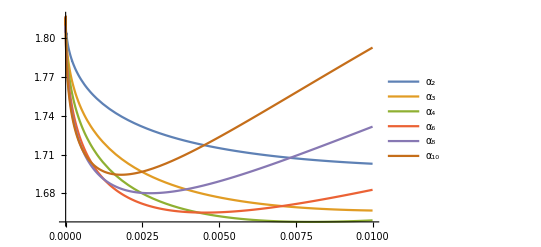

```mathematica
Plot[{alphas[2,1-2x,1],alphas[3,1-2x,1],alphas[4,1-2x,1],alphas[6,1-2x,1],alphas[8,1-2x,1],alphas[10,1-2x,1]},{x,0,0.01}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10"}, PlotRange->All]
```

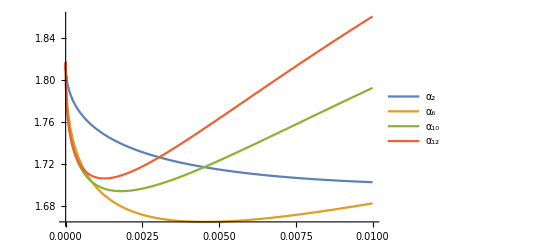

```mathematica
Plot[{alphas[2,1-2x,1],alphas[6,1-2x,1],alphas[10,1-2x,1], alphas[12,1-2x,1]},{x,0,0.01}, PlotLegends->{"α_2","α_6","α_10","α_12"}, PlotRange->All]
```

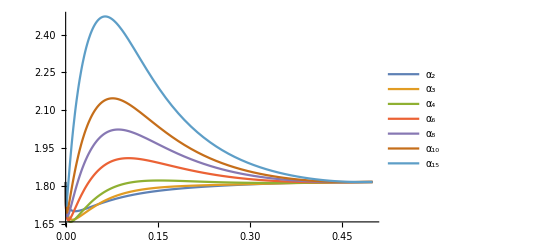

```mathematica
Plot[{alphas[2,1-2x,1],alphas[3,1-2x,1],alphas[4,1-2x,1],alphas[6,1-2x,1],alphas[8,1-2x,1],alphas[10,1-2x,1],alphas[15,1-2x,1]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10","α_15"}, PlotRange->All]
```

### k=0.9

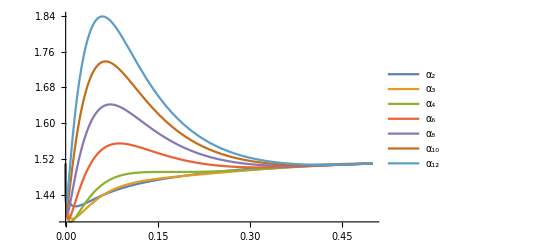

```mathematica
Plot[{alphas[2,1-2x,0.9],alphas[3,1-2x,0.9],alphas[4,1-2x,0.9],alphas[6,1-2x,0.9],alphas[8,1-2x,0.9], alphas[10,1-2x,0.9],alphas[12,1-2x,0.9]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

### k=0.8

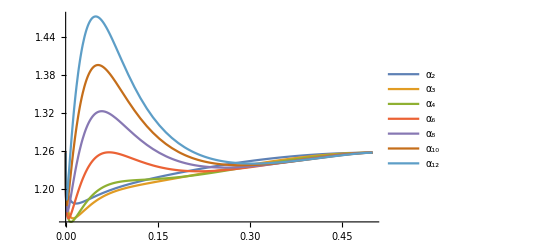

```mathematica
Plot[{alphas[2,1-2x,0.8],alphas[3,1-2x,0.8],alphas[4,1-2x,0.8],alphas[6,1-2x,0.8],alphas[8,1-2x,0.8], alphas[10,1-2x,0.8],alphas[12,1-2x,0.8]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

### K=0.7

```mathematica
N[alphasRC[0.7]]
```

1.04783

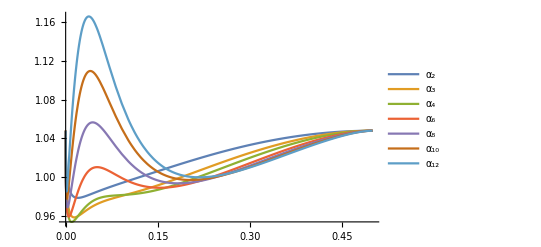

```mathematica
Plot[{alphas[2,1-2x,0.7],alphas[3,1-2x,0.7],alphas[4,1-2x,0.7],alphas[6,1-2x,0.7],alphas[8,1-2x,0.7], alphas[10,1-2x,0.7],alphas[12,1-2x,0.7]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

### K=0.6

```mathematica
N[alphasRC[0.6]]
```

0.871671

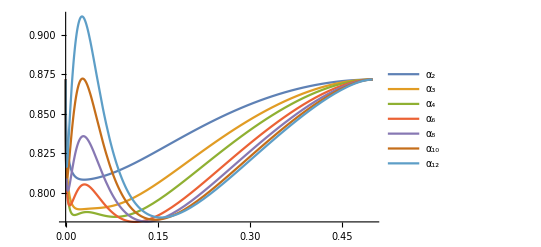

```mathematica
Plot[{alphas[2,1-2x,0.6],alphas[3,1-2x,0.6],alphas[4,1-2x,0.6],alphas[6,1-2x,0.6],alphas[8,1-2x,0.6], alphas[10,1-2x,0.6],alphas[12,1-2x,0.6]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

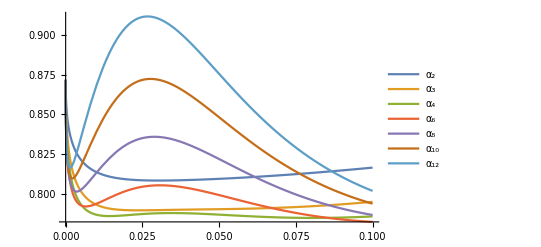

```mathematica
Plot[{alphas[2,1-2x,0.6],alphas[3,1-2x,0.6],alphas[4,1-2x,0.6],alphas[6,1-2x,0.6],alphas[8,1-2x,0.6], alphas[10,1-2x,0.6],alphas[12,1-2x,0.6]},{x,0,0.1}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

### K=0.5

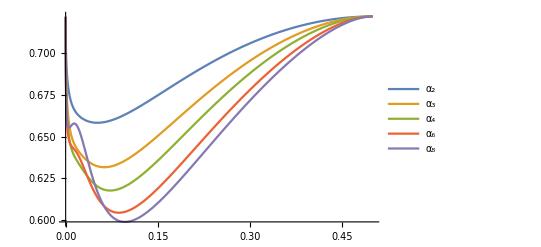

```mathematica
Plot[{alphas[2,1-2x,0.5],alphas[3,1-2x,0.5],alphas[4,1-2x,0.5],alphas[6,1-2x,0.5],alphas[8,1-2x,0.5]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8"}, PlotRange->All]
```

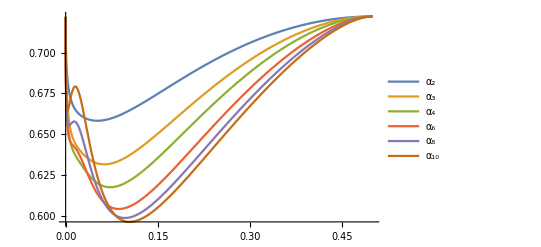

```mathematica
Plot[{alphas[2,1-2x,0.5],alphas[3,1-2x,0.5],alphas[4,1-2x,0.5],alphas[6,1-2x,0.5],alphas[8,1-2x,0.5], alphas[10,1-2x,0.5]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10"}, PlotRange->All]
```

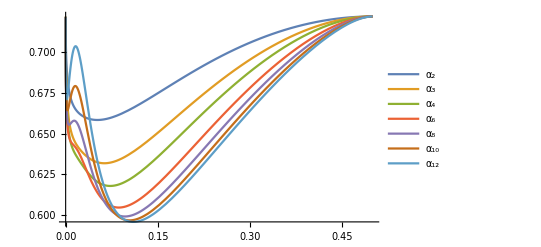

```mathematica
Plot[{alphas[2,1-2x,0.5],alphas[3,1-2x,0.5],alphas[4,1-2x,0.5],alphas[6,1-2x,0.5],alphas[8,1-2x,0.5], alphas[10,1-2x,0.5],alphas[12,1-2x,0.5]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

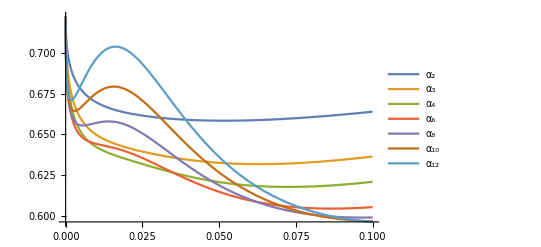

```mathematica
Plot[{alphas[2,1-2x,0.5],alphas[3,1-2x,0.5],alphas[4,1-2x,0.5],alphas[6,1-2x,0.5],alphas[8,1-2x,0.5], alphas[10,1-2x,0.5],alphas[12,1-2x,0.5]},{x,0,0.1}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

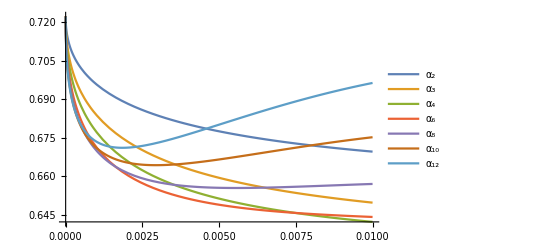

```mathematica
Plot[{alphas[2,1-2x,0.5],alphas[3,1-2x,0.5],alphas[4,1-2x,0.5],alphas[6,1-2x,0.5],alphas[8,1-2x,0.5], alphas[10,1-2x,0.5],alphas[12,1-2x,0.5]},{x,0,0.01}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

### K=0.4

```mathematica
N[alphasRC[0.4]]
```

0.593211

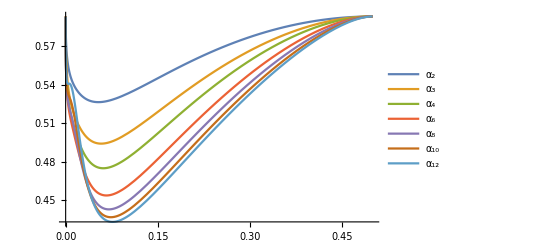

```mathematica
Plot[{alphas[2,1-2x,0.4],alphas[3,1-2x,0.4],alphas[4,1-2x,0.4],alphas[6,1-2x,0.4],alphas[8,1-2x,0.4], alphas[10,1-2x,0.4],alphas[12,1-2x,0.4]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

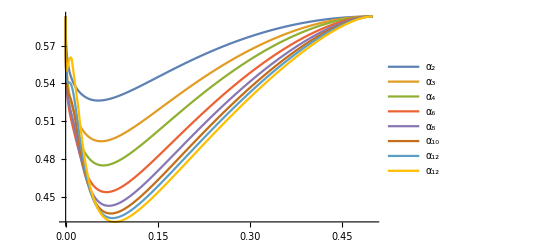

```mathematica
Plot[{alphas[2,1-2x,0.4],alphas[3,1-2x,0.4],alphas[4,1-2x,0.4],alphas[6,1-2x,0.4],alphas[8,1-2x,0.4], alphas[10,1-2x,0.4],alphas[12,1-2x,0.4],alphas[15,1-2x,0.4]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12","α_12","α_15"}, PlotRange->All]
```

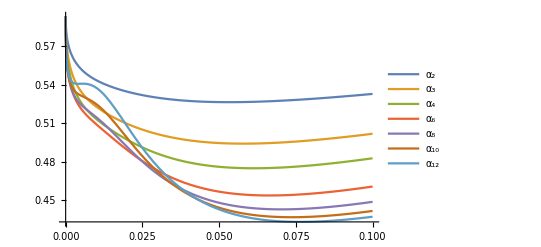

```mathematica
Plot[{alphas[2,1-2x,0.4],alphas[3,1-2x,0.4],alphas[4,1-2x,0.4],alphas[6,1-2x,0.4],alphas[8,1-2x,0.4], alphas[10,1-2x,0.4],alphas[12,1-2x,0.4]},{x,0,0.1}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

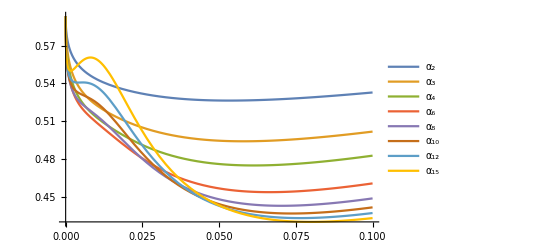

```mathematica
Plot[{alphas[2,1-2x,0.4],alphas[3,1-2x,0.4],alphas[4,1-2x,0.4],alphas[6,1-2x,0.4],alphas[8,1-2x,0.4], alphas[10,1-2x,0.4],alphas[12,1-2x,0.4],alphas[15,1-2x,0.4]},{x,0,0.1}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12","α_15"}, PlotRange->All]
```

### K=0.3

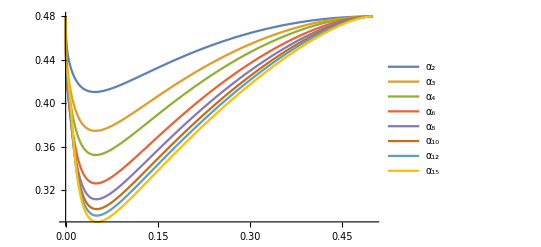

```mathematica
Plot[{alphas[2,1-2x,0.3],alphas[3,1-2x,0.3],alphas[4,1-2x,0.3],alphas[6,1-2x,0.3],alphas[8,1-2x,0.3], alphas[10,1-2x,0.3],alphas[12,1-2x,0.3],alphas[15,1-2x,0.3]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12","α_15"}, PlotRange->All]
```

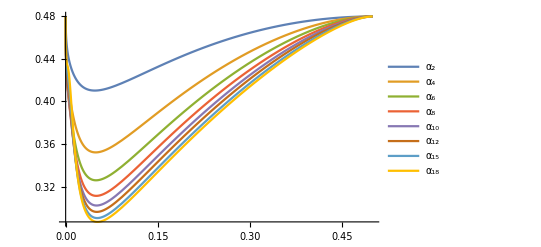

```mathematica
Plot[{alphas[2,1-2x,0.3],alphas[4,1-2x,0.3],alphas[6,1-2x,0.3],alphas[8,1-2x,0.3], alphas[10,1-2x,0.3],alphas[12,1-2x,0.3],alphas[15,1-2x,0.3], alphas[18,1-2x,0.3]},{x,0,0.5}, PlotLegends->{"α_2","α_4","α_6","α_8","α_10", "α_12","α_15","α_18"}, PlotRange->All]
```

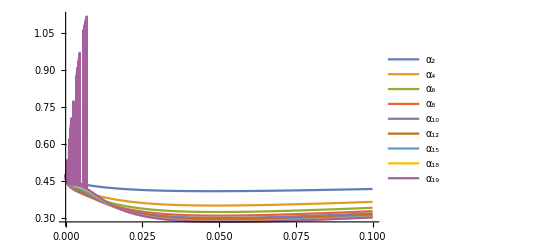

```mathematica
Plot[{alphas[2,1-2x,0.3],alphas[4,1-2x,0.3],alphas[6,1-2x,0.3],alphas[8,1-2x,0.3], alphas[10,1-2x,0.3],alphas[12,1-2x,0.3],alphas[15,1-2x,0.3], alphas[18,1-2x,0.3],alphas[19,1-2x,0.3]},{x,0,0.1}, PlotLegends->{"α_2","α_4","α_6","α_8","α_10", "α_12","α_15","α_18","α_19"}, PlotRange->All]
```

### K=0.2

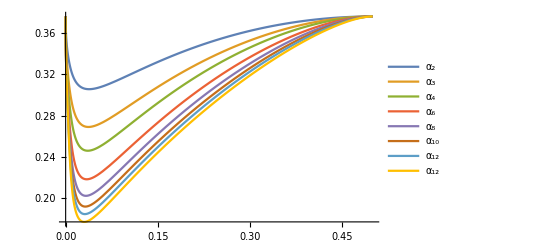

```mathematica
Plot[{alphas[2,1-2x,0.2],alphas[3,1-2x,0.2],alphas[4,1-2x,0.2],alphas[6,1-2x,0.2],alphas[8,1-2x,0.2], alphas[10,1-2x,0.2],alphas[12,1-2x,0.2],alphas[15,1-2x,0.2]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12","α_12","α_15"}, PlotRange->All]
```

### K=0.1

```mathematica
N[alphasRC[0.1]]
```

0.273967

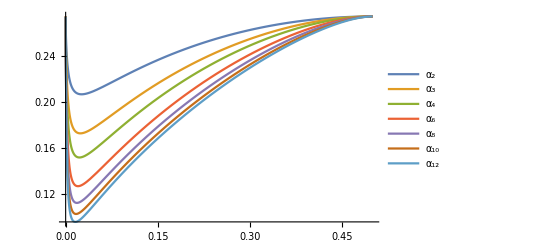

```mathematica
Plot[{alphas[2,1-2x,0.1],alphas[3,1-2x,0.1],alphas[4,1-2x,0.1],alphas[6,1-2x,0.1],alphas[8,1-2x,0.1], alphas[10,1-2x,0.1],alphas[12,1-2x,0.1]},{x,0,0.5}, PlotLegends->{"α_2","α_3","α_4","α_6","α_8","α_10", "α_12"}, PlotRange->All]
```

## Lower Bound, Second Moment computations

### Y=2, Second Moment Lower Bound (similar to Daudé, Mézard, Mora, Zecchina 2007 but f1 and f2 different...)

In the second moment we’ll have to work out the overlap for two couple of solutions. First of all, let’s show that when the two pairs are uncorrelated then the gaussian integral we have to perform splits in the gaussian integrals of two uncorrelated bivariate gaussians for a*. 
(Notation here differs respect to calculations on paper. Here the second pair is indicated with capitalized letters, there you used tilde.)

```mathematica
dw1W1 = a2+a3+a6+a7 
dw1W2 = a1+a3+a5+a7  
dw2W1 = a2+a3+a4+a5
dw2W2 = a1+a3+a4+a6
```

a2+a3+a6+a7

a1+a3+a5+a7

a2+a3+a4+a5

a1+a3+a4+a6

```mathematica
qw1W1 = 1-2 dw1W1
qw1W2 = 1-2 dw1W2 
qw2W1 = 1-2 dw2W1
qw2W2 = 1-2 dw2W2
```

1-2 (a2+a3+a6+a7)

1-2 (a1+a3+a5+a7)

1-2 (a2+a3+a4+a5)

1-2 (a1+a3+a4+a6)

```mathematica
Σ={{1,1-2x,qw1W1,qw1W2},
     {1-2x,1,qw2W1,qw2W2},
     {qw1W1,qw2W1,1,1-2x },
     {qw1W2, qw2W2,1-2x,1}}
```

{{1,1-2 x,1-2 (a2+a3+a6+a7),1-2 (a1+a3+a5+a7)},{1-2 x,1,1-2 (a2+a3+a4+a5),1-2 (a1+a3+a4+a6)},{1-2 (a2+a3+a6+a7),1-2 (a2+a3+a4+a5),1,1-2 x},{1-2 (a1+a3+a5+a7),1-2 (a1+a3+a4+a6),1-2 x,1}}

```mathematica
MatrixForm[Σ]
```

```mathematica
({{1, 1-2 x, 1-2 (a2+a3+a6+a7), 1-2 (a1+a3+a5+a7)}, {1-2 x, 1, 1-2 (a2+a3+a4+a5), 1-2 (a1+a3+a4+a6)}, {1-2 (a2+a3+a6+a7), 1-2 (a2+a3+a4+a5), 1, 1-2 x}, {1-2 (a1+a3+a5+a7), 1-2 (a1+a3+a4+a6), 1-2 x, 1}})
```

{{1,1-2 x,1-2 (a2+a3+a6+a7),1-2 (a1+a3+a5+a7)},{1-2 x,1,1-2 (a2+a3+a4+a5),1-2 (a1+a3+a4+a6)},{1-2 (a2+a3+a6+a7),1-2 (a2+a3+a4+a5),1,1-2 x},{1-2 (a1+a3+a5+a7),1-2 (a1+a3+a4+a6),1-2 x,1}}

```mathematica
FullSimplify[MatrixForm[Σ]/. {a3->(1-x)^2/2,a1-> x(1-x)/2,a2->x(1-x)/2,a4->x(1-x)/2,a7->x(1-x)/2,
				a5->x^2/2,a6->x^2/2 }]
```

(1 | 1-2 x | 0 | 0
1-2 x | 1 | 0 | 0
0 | 0 | 1 | 1-2 x
0 | 0 | 1-2 x | 1)

We have now to check for which α we have an absolute maximum in a*.
We start from the first derivative, we have to check if this is equal to 0 in a*.

```mathematica
MatrixForm[Σ]
```

(1 | 1-2 x | 1-2 (a2+a3+a6+a7) | 1-2 (a1+a3+a5+a7)
1-2 x | 1 | 1-2 (a2+a3+a4+a5) | 1-2 (a1+a3+a4+a6)
1-2 (a2+a3+a6+a7) | 1-2 (a2+a3+a4+a5) | 1 | 1-2 x
1-2 (a1+a3+a5+a7) | 1-2 (a1+a3+a4+a6) | 1-2 x | 1)

```mathematica
FullSimplify[MatrixForm[Σ]/. {a7-> a1+a2-a4,a6->x-a1-a2-a5,a0->1-a1-a2-a3-x }]
```

(1 | 1-2 x | 1-2 (a2+a3-a4-a5+x) | 1-2 (2 a1+a2+a3-a4+a5)
1-2 x | 1 | 1-2 (a2+a3+a4+a5) | 1-2 (-a2+a3+a4-a5+x)
1-2 (a2+a3-a4-a5+x) | 1-2 (a2+a3+a4+a5) | 1 | 1-2 x
1-2 (2 a1+a2+a3-a4+a5) | 1-2 (-a2+a3+a4-a5+x) | 1-2 x | 1)

### Final form of Σ as funciton of just a1,...,a5. “Check” when covariances are RS ones.

```mathematica
mm = {{0,1,1,-1,-1},{2,1,1,-1,1},{0,1,1,1,1},{0,-1,1,1,-1}}; MatrixForm[mm]
```

(0 | 1 | 1 | -1 | -1
2 | 1 | 1 | -1 | 1
0 | 1 | 1 | 1 | 1
0 | -1 | 1 | 1 | -1)

```mathematica
m = 2*mm; MatrixForm[m]
```

(0 | 2 | 2 | -2 | -2
4 | 2 | 2 | -2 | 2
0 | 2 | 2 | 2 | 2
0 | -2 | 2 | 2 | -2)

```mathematica
bb = {1-2*x-q0, 1-q0, 1-q0 ,1-2*x-q0 }; MatrixForm[bb]
```

(1-q0-2 x
1-q0
1-q0
1-q0-2 x)

```mathematica
LinearSolve[m,bb]
```

{x/2,x/2,1/2 (1-q0-2 x),x/2,0}

```mathematica
NullSpace[m]
```

{{-1,-1,1,-1,1}}

```mathematica
ma = m.{a1,a2,a3,a4,a5}
```

{2 a2+2 a3-2 a4-2 a5,4 a1+2 a2+2 a3-2 a4+2 a5,2 a2+2 a3+2 a4+2 a5,-2 a2+2 a3+2 a4-2 a5}

```mathematica
ma = MatrixForm[ma]
```

(2 a2+2 a3-2 a4-2 a5
4 a1+2 a2+2 a3-2 a4+2 a5
2 a2+2 a3+2 a4+2 a5
-2 a2+2 a3+2 a4-2 a5)

```mathematica
FullSimplify[ma/.{a1-> x/2-η,a2-> x/2-η, a3-> 1/2*(1-q0-2x)+η,a4-> x/2-η,a5->η}]
```

(1-q0-2 x
1-q0
1-q0
1-q0-2 x)

```mathematica
{a1+a2-a4, a1+a2+a5,a1+a2+a3}/.{a1-> x/2-η,a2-> x/2-η, a3-> 1/2*(1-q0-2x)+η,a4-> x/2-η,a5->η}; MatrixForm[%]
```

(1-q0-2 x
1-q0
1-q0
1-q0-2 x)

```mathematica
FullSimplify[Reduce[{1/2(1-q0-2 x)+x-η≤1-x},η],Assumptions->{0≤q0≤1,0≤x≤1/2}]
```

1+q0+2 η≥2 x

```mathematica
Reduce[{1/2(1-q0-2 x)+x-η≤1-x},η]
```

(q0|x)∈ℝ&&η≥1/2 (-1-q0+2 x)

```mathematica
FullSimplify[Reduce[{0≤1/2 (1-q0-2 x)+η≤1,0≤η≤x/2,η≥(-1-q0+2x)/2  },η], Assumptions->{0<q0≤1,0<x<1/2}]
```

(x==2 η&&q0+x==1)||(x≥2 η&&((q0+2 x>1&&q0+x<1&&q0+2 x≤1+2 η)||(η≥0&&q0+2 x≤1)))

Solution:	η≤x/2  con la

### Try to rewrite integral over 5-dim symplex to 4-dim symplex:

```mathematica
mm = {{0,1,1,-1,-1},{2,1,1,-1,1},{0,1,1,1,1},{0,-1,1,1,-1}}; MatrixForm[mm]
```

(0 | 1 | 1 | -1 | -1
2 | 1 | 1 | -1 | 1
0 | 1 | 1 | 1 | 1
0 | -1 | 1 | 1 | -1)

```mathematica
m = 2*mm; MatrixForm[m]
```

(0 | 2 | 2 | -2 | -2
4 | 2 | 2 | -2 | 2
0 | 2 | 2 | 2 | 2
0 | -2 | 2 | 2 | -2)

```mathematica
bb = {1-2*x-q1, 1-q2, 1-q3 ,1-2*x-q4 }; MatrixForm[bb]
```

(1-q1-2 x
1-q2
1-q3
1-q4-2 x)

```mathematica
LinearSolve[m,bb]
```

{1/4 (q1-q2+2 x),1/4 (-q3+q4+2 x),1/4 (2-q1-q4-4 x),1/4 (q1-q3+2 x),0}

```mathematica
NullSpace[m]
```

{{-1,-1,1,-1,1}}

```mathematica
ma = m.{a1,a2,a3,a4,a5}
```

{2 a2+2 a3-2 a4-2 a5,4 a1+2 a2+2 a3-2 a4+2 a5,2 a2+2 a3+2 a4+2 a5,-2 a2+2 a3+2 a4-2 a5}

```mathematica
ma = MatrixForm[ma]
```

(2 a2+2 a3-2 a4-2 a5
4 a1+2 a2+2 a3-2 a4+2 a5
2 a2+2 a3+2 a4+2 a5
-2 a2+2 a3+2 a4-2 a5)

```mathematica
FullSimplify[ma/.{a1-> 1/4 (q1-q2+2 x)-η,a2-> 1/4 (-q3+q4+2 x)-η, a3-> 1/4 (2-q1-q4-4 x)+η,a4-> 1/4 (q1-q3+2 x)-η,a5->η}]
```

(1-q1-2 x
1-q2
1-q3
1-q4-2 x)

What is called aa1, aa2, ... is (a^*)_1, (a^*)_2,... in my notes. Is simply the generic form of a solution.

```mathematica
aa1 =  1/4 (q1-q2+2 x)-η
```

1/4 (q1-q2+2 x)-η

```mathematica
aa2 = 1/4 (-q3+q4+2 x)-η
```

1/4 (-q3+q4+2 x)-η

```mathematica
aa3 = 1/4 (2-q1-q4-4 x)+η
```

1/4 (2-q1-q4-4 x)+η

```mathematica
aa4 =1/4 (q1-q3+2 x)-η
```

1/4 (q1-q3+2 x)-η

```mathematica
aa5 = η
```

η

```mathematica
FullSimplify[aa1+aa2-aa4]
```

1/4 (-q2+q4+2 x-4 η)

```mathematica
FullSimplify[aa1+aa2+aa5]
```

1/4 (q1-q2-q3+q4+4 x-4 η)

```mathematica
FullSimplify[aa1+aa2+aa3]
```

1/4 (2-q2-q3-4 η)

```mathematica
Reduce[{0≤1/4 (q1-q2+2 x)-η≤ 1,0≤ 1/4 (-q3+q4+2 x)-η≤1, 0≤1/4 (2-q1-q4-4 x)+η≤1,0≤1/4 (q1-q3+2 x)-η≤1,0≤η≤1, 0≤ 1/4 (-q2+q4+2 x-4 η)≤1,
0≤ 1/4 (q1-q2-q3+q4+4 x-4 η)≤ x, 0≤ 1/4 (2-q2-q3-4 η)≤ 1-x, 0≤x≤1},{q1,q2,q3,q4,η}]
```

$Aborted

```mathematica
Reduce[{0≤1/4 (q1-q2+2 x)-η≤ 1,0≤ 1/4 (-q3+q4+2 x)-η≤1, 0≤1/4 (2-q1-q4-4 x)+η≤1,0≤1/4 (q1-q3+2 x)-η≤1,0≤η≤1, 0≤ 1/4 (-q2+q4+2 x-4 η)≤1,
0≤ 1/4 (q1-q2-q3+q4+4 x-4 η)≤ x, 0≤ 1/4 (2-q2-q3-4 η)≤ 1-x, 0≤x≤1},{η}]
```

Follow constraints # 1:

```mathematica
Reduce[0≤1/4 (q1-q2+2 x)-η≤ 1, {η}]
Reduce[0≤ 1/4 (-q3+q4+2 x)-η≤1, {η}]
Reduce[ 0≤1/4 (2-q1-q4-4 x)+η≤1, {η}]
Reduce[0≤1/4 (q1-q3+2 x)-η≤1, {η}]
Reduce[0≤η≤ 1, {η}]
```

(q1|q2|x)∈ℝ&&1/4 (-4+q1-q2+2 x)≤η≤1/4 (q1-q2+2 x)

(q3|q4|x)∈ℝ&&1/4 (-4-q3+q4+2 x)≤η≤1/4 (-q3+q4+2 x)

(q1|q4|x)∈ℝ&&1/4 (-2+q1+q4+4 x)≤η≤1/4 (2+q1+q4+4 x)

(q1|q3|x)∈ℝ&&1/4 (-4+q1-q3+2 x)≤η≤1/4 (q1-q3+2 x)

0≤η≤1

Constraint # 2:

```mathematica
Reduce[0≤ 1/4 (-q2+q4+2 x-4 η)≤1, {η}]
```

(q2|q4|x)∈ℝ&&1/4 (-4-q2+q4+2 x)≤η≤1/4 (-q2+q4+2 x)

Constraint # 3:

```mathematica
Reduce[0≤ 1/4 (q1-q2-q3+q4+4 x-4 η)≤ x, {η}]
```

(q1|q2|q3|q4)∈ℝ&&((x==0&&η==1/4 (q1-q2-q3+q4))||(x>0&&1/4 (q1-q2-q3+q4)≤η≤1/4 (q1-q2-q3+q4+4 x)))

Constraint # 4:

```mathematica
Reduce[0≤ 1/4 (2-q2-q3-4 η)≤ 1-x, {η}]
```

(q2|q3)∈ℝ&&((x<1&&1/4 (-2-q2-q3+4 x)≤η≤1/4 (2-q2-q3))||(x==1&&η==1/4 (2-q2-q3)))

### Check of invertibility for Σ:

```mathematica
Inverse[({{1, 1-2 x, q0, q0}, {1-2 x, 1, q0, q0}, {q0, q0, 1, 1-2 x}, {q0, q0, 1-2 x, 1}})]
```

{{(4 x-4 q0^2 x-4 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),(-4 x+4 q0^2 x+12 x^2-8 x^3)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),-(4 q0 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),-(4 q0 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4)},{(-4 x+4 q0^2 x+12 x^2-8 x^3)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),(4 x-4 q0^2 x-4 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),-(4 q0 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),-(4 q0 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4)},{-(4 q0 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),-(4 q0 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),(4 x-4 q0^2 x-4 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),(-4 x+4 q0^2 x+12 x^2-8 x^3)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4)},{-(4 q0 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),-(4 q0 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),(-4 x+4 q0^2 x+12 x^2-8 x^3)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4),(4 x-4 q0^2 x-4 x^2)/(16 x^2-16 q0^2 x^2-32 x^3+16 x^4)}}

Notice that the inverse seems feasible to do, just when x is very small one could have problems.

```mathematica
({{1, 1-2 xx, q0, q0}, {1-2 xx, 1, q0, q0}, {q0, q0, 1, 1-2 xx}, {q0, q0, 1-2 xx, 1}})//.{xx-> 0.01,q0-> 1.}
```

{{1,0.98,1.,1.},{0.98,1,1.,1.},{1.,1.,1,0.98},{1.,1.,0.98,1}}

```mathematica
MatrixForm[%]
```

(1 | 0.98 | 1. | 1.
0.98 | 1 | 1. | 1.
1. | 1. | 1 | 0.98
1. | 1. | 0.98 | 1)

```mathematica
Inverse[%]
```

{{12.5628,-37.4372,12.5628,12.5628},{-37.4372,12.5628,12.5628,12.5628},{12.5628,12.5628,12.5628,-37.4372},{12.5628,12.5628,-37.4372,12.5628}}

```mathematica
MatrixForm[%]
```

(12.5628 | -37.4372 | 12.5628 | 12.5628
-37.4372 | 12.5628 | 12.5628 | 12.5628
12.5628 | 12.5628 | 12.5628 | -37.4372
12.5628 | 12.5628 | -37.4372 | 12.5628)

### Study of Second Moment with expansion for δq_1 → 0 only for the optimization of Φ_I+Φ_S, y=2

```mathematica
g[z_]:=Exp[-z^2/2]/Sqrt[2π]
H[z_]:=1/2Erfc[z/Sqrt[2]]
```

```mathematica
ΦE0[q0_?NumericQ,dq1_?NumericQ,K_,z_]:=NIntegrate[g[t](H[-K/(√dq1)+(√q0 z+√(1-dq1-q0)t)/(√dq1)]-H[K/(√dq1)+(√q0 z+√(1-dq1-q0)t)/(√dq1)])^2,{t,-∞,∞}]^2

ΦE[q0_?NumericQ,dq1_?NumericQ,K_] := Log[NIntegrate[g[z]ΦE0[q0,dq1,K,z], {z,-∞,∞}]]
```

```mathematica
Subscript[Φ, S][qh0_,qh1_]:=Log[2]+Log[2+4 ⅇ^(2qh1)+ⅇ^(4qh0+4qh1)+ⅇ^(4qh1-4qh0)]
```

```mathematica
Subscript[Φ, I][q0_,qh0_,dq1_,qh1_]:=-2qh1-4q0 qh0-2(1-dq1)qh1
```

```mathematica
Subscript[Φ1, den][q0_, qh0_, dq1_, qh1_,α_,k_]:=Subscript[Φ, I][q0,qh0,dq1,qh1]+Subscript[Φ, S][qh0,qh1]+α ΦE[q0,dq1,k]
```

```mathematica
Subscript[OptΦ1, den][q0_,dq1_,α_,k_]:= Subscript[Φ1, den][q0,1/4 Log[√((1+q0)/(1-q0))], dq1,1/2 Log[(2 √(1-q0^2))/dq1] ,α,k]
```

```mathematica
Table[{q0,Subscript[OptΦ1, den][q0,0.0001,0.3,1]},{q0,0.1,0.9,0.1 }]
```

{{0.1,1.1517},{0.2,1.13888},{0.3,1.11722},{0.4,1.08624},{0.5,1.04517},{0.6,0.992746},{0.7,0.926901},{0.8,0.843895},{0.9,0.735976}}

```mathematica
Table[{dq1,Subscript[OptΦ, den][0.1,dq1,0.3,1]},{dq1,0.00001,0.0001,0.00001 }]
```

{{0.00001,1.1533},{0.00002,1.15348},{0.00003,1.15365},{0.00004,1.1538},{0.00005,1.15394},{0.00006,1.15408},{0.00007,1.15421},{0.00008,1.15435},{0.00009,1.15447},{0.0001,1.1546}}

```mathematica
Table[{dq1,Subscript[OptΦ1, den][0.1,dq1,0.3,1]},{dq1,0.00001,0.0001,0.00001 }]
```

{{0.00001,1.15238},{0.00002,1.15219},{0.00003,1.15206},{0.00004,1.15197},{0.00005,1.1519},{0.00006,1.15184},{0.00007,1.15179},{0.00008,1.15176},{0.00009,1.15173},{0.0001,1.1517}}

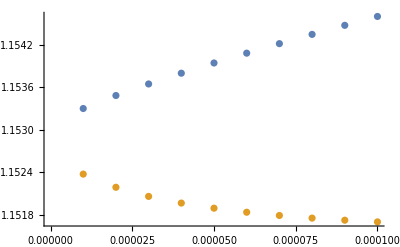

```mathematica
ListPlot[{%106,%107}]
```

```mathematica
Table[{dq1,Subscript[OptΦ, den][0.1,dq1,0.3,1]},{dq1,0.000001,0.00001,0.000001 }]
```

{{1.×10^-6,1.15308},{2.×10^-6,1.15311},{3.×10^-6,1.15314},{4.×10^-6,1.15317},{5.×10^-6,1.15319},{6.×10^-6,1.15322},{7.×10^-6,1.15324},{8.×10^-6,1.15326},{9.×10^-6,1.15328},{0.00001,1.1533}}

```mathematica
Table[{dq1,Subscript[OptΦ1, den][0.1,dq1,0.3,1]},{dq1,0.000001,0.00001,0.000001 }]
```

{{1.×10^-6,1.15278},{2.×10^-6,1.15269},{3.×10^-6,1.15263},{4.×10^-6,1.15258},{5.×10^-6,1.15254},{6.×10^-6,1.1525},{7.×10^-6,1.15247},{8.×10^-6,1.15244},{9.×10^-6,1.15241},{0.00001,1.15238}}

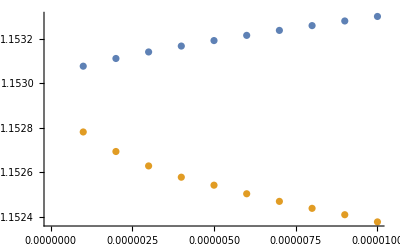

```mathematica
ListPlot[{%109,%110}]
```

```mathematica
With[{α=Range[1.4,2.5,0.1]},Plot[Subscript[OptΦ1, den][q0,0.001,α,1],{q0,0,1}]]
```

NIntegrate::inumr: The integrand (ⅇ^(-t^2/2) (1/2 Erfc[(-31.6228+Times[«2»])/(√2)]-1/2 Erfc[(«19»+«1»)/(√2)])^2)/(√(2 π)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
FullSimplify[Subscript[Φ, I][q0,1/4 Log[√((1+q0)/(1-q0))],1-q1,1/2 Log[(2 √(1-q0^2))/(1-q1)]]+Subscript[Φ, S][1/4 Log[√((1+q0)/(1-q0))],1/2 Log[(2 √(1-q0^2))/(1-q1)]]]
```

-1/2 q0 Log[-(1+q0)/(-1+q0)]+Log[(4 (4 √((1+q0)/(1-q0))-4 q0 √((1+q0)/(1-q0))-4 √(1-q0^2) (-1+q1)+(-1+q1)^2))/(-1+q1)^2]-(1+q1) Log[-(2 √(1-q0^2))/(-1+q1)]

```mathematica
FullSimplify[4 √((1+q0)/(1-q0))-4 q0 √((1+q0)/(1-q0))-4 √(1-q0^2) (-1+q1)+(-1+q1)^2,Assumptions->q0<1]
```

4 √((1+q0)/(1-q0))-4 q0 √((1+q0)/(1-q0))-4 √(1-q0^2) (-1+q1)+(-1+q1)^2

```mathematica
FullSimplify[4 √(1-q0^2)-4 √(1-q0^2) (-1+q1)+(-1+q1)^2]
```

8 √(1-q0^2)+(-1+q1)^2-4 √(1-q0^2) q1

### Y=1, Second Moment Lower Bound (check results paper by Aubin, Perkins, Zdeborova 2019)

Here I show that the quantity q_(r,K)(β ) (Eq. 6) has first derivative equal to 0 in in 1/2.

```mathematica
qrect[ β_,K_]:=1/(2π)Integrate[Integrate[Exp[-(x^2+y^2)/2],{x,(-K+(1-2β)y)/(2√(β(1-β))),(+K+(1-2β)y)/(2√(β(1-β)))}],
					{y,-K,K}]
```

```mathematica
qrect[0.6,∞]
```

1

```mathematica
Dqrect[β_,K_]= D[qrect[β,K], β]
```

(ⅇ^(K^2/(2 (-1+β))) (-1+ⅇ^((K^2 (2-4 β))/(4 (-1+β) β))))/(π √(-(-1+β) β))

```mathematica
Dqrect[0.5,K]
```

0.

```mathematica
Subscript[H, 2][β_] := -β Log[β]-(1-β)Log[1-β]
```

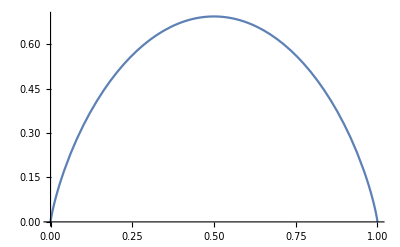

```mathematica
Plot[Subscript[H, 2][β],{β,0,1}]
```

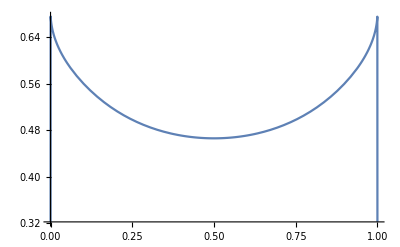

```mathematica
Plot[qrect[β,1],{β,0,1}]
```

Here just follows an example with α = 1 to see that the function F_(r,K,α=1) (β ) has a maximum in 1/2.

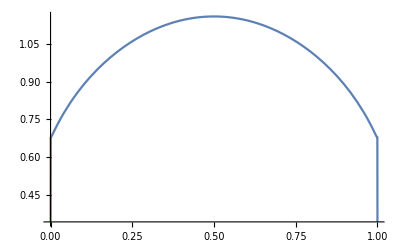

```mathematica
Plot[Subscript[H, 2][β]+qrect[β,1],{β,0,1}]
```

Try same thing but using function PDF[] of Mathematica, just an experiment for what comes later. Ignore this part.

```mathematica
PDF[MultinormalDistribution[{0,0},{{1,2β-1},{2β-1,1}}],{x,y}]
```

ⅇ^(1/2 (-(y (-x-y+2 x β))/(4 (-1+β) β)-(x (-x-y+2 y β))/(4 (-1+β) β)))/(2 π √(4 β-4 β^2))

```mathematica
qrect2[ β_,K_]:=Integrate[Integrate[PDF[MultinormalDistribution[{0,0},{{1,2β-1},{2β-1,1}}],{x,y}]  ,{x,-K,K}],
					{y,-K,K}]
```

```mathematica
Dqrect2[β_,K_]= D[qrect2[β,K], β]
```

(ⅇ^(K^2/(2 (-1+β))) (-1+ⅇ^((K^2 (2-4 β))/(4 (-1+β) β))))/(π √(-(-1+β) β))

```mathematica
Dqrect2[0.5,K]
```

0.

Ok, I get the same results.

#### Use Cholesky to rewrite integral q_K(β)

Here I use Cholesky to try to get the integral in paper for q_K(β). Here this integral is called qrect above.

```mathematica
ClearAll["Global`*"]
```

```mathematica
Σ={{1,2β-1},{2β-1,1}};
Assumptions-> β∈Reals;
MatrixForm[Σ]
```

(1 | -1+2 β
-1+2 β | 1)

```mathematica
cU=FullSimplify[CholeskyDecomposition[Σ ],Assumptions->β∈Reals]
```

{{1,-1+2 β},{0,2 √(-(-1+β) β)}}

```mathematica
cL = Transpose[cU]
```

{{1,0},{-1+2 β,2 √(-(-1+β) β)}}

```mathematica
MatrixForm[cL]
 MatrixForm[cU]
```

(1 | 0
-1+2 β | 2 √(-(-1+β) β))

(1 | -1+2 β
0 | 2 √(-(-1+β) β))

```mathematica
FullSimplify[MatrixForm[cL.cU]]
```

(1 | -1+2 β
-1+2 β | 1)

```mathematica
MatrixForm[invcL=Inverse[cL]]
```

(1 | 0
(1-2 β)/(2 √(-(-1+β) β)) | 1/(2 √(-(-1+β) β)))

From y=cL^-1 z   iff  cL y= z and from the second we have just to impose all entries between -k and k to find the new domain of integration in the y’s. The result is exactly like in the paper.

```mathematica
FullSimplify[MatrixForm[invcL=Inverse[cL]]/.{ β->1-x}]
```

(1 | 0
(-1+2 x)/(2 √(-(-1+x) x)) | 1/(2 √(-(-1+x) x)))

```mathematica
FullSimplify[MatrixForm[cL]/.{ β->1-x}]
```

(1 | 0
1-2 x | 2 √(-(-1+x) x))

### Expansion Second Moment - checks with results of Lenka

In my expansion of the second moment with coupled replicas I would like to see if in the limit δq_1→ 1 I can obtain the result of Zdeborova for their perceptron.

```mathematica
Plot[qrect[(q0+1)/2,1],{q0,-1,1}]
```

$Aborted

```mathematica
Tqrect =Table[{q0,qrect[(q0+1)/2,1]},{q0, -0.9,0.9,0.1}]
```

{{-0.9,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[1.62221-1.45999 y]+1.25331 Erf[1.62221+1.45999 y])ⅆy)/(2 π)},{-0.8,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[1.17851-0.942809 y]+1.25331 Erf[1.17851+0.942809 y])ⅆy)/(2 π)},{-0.7,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.990148-0.693103 y]+1.25331 Erf[0.990148+0.693103 y])ⅆy)/(2 π)},{-0.6,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.883883-0.53033 y]+1.25331 Erf[0.883883+0.53033 y])ⅆy)/(2 π)},{-0.5,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.816497-0.408248 y]+1.25331 Erf[0.816497+0.408248 y])ⅆy)/(2 π)},{-0.4,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.771517-0.308607 y]+1.25331 Erf[0.771517+0.308607 y])ⅆy)/(2 π)},{-0.3,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.741249-0.222375 y]+1.25331 Erf[0.741249+0.222375 y])ⅆy)/(2 π)},{-0.2,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.721688-0.144338 y]+1.25331 Erf[0.721688+0.144338 y])ⅆy)/(2 π)},{-0.1,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.710669-0.0710669 y]+1.25331 Erf[0.710669+0.0710669 y])ⅆy)/(2 π)},{0.,0.466065},{0.1,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.710669-0.0710669 y]+1.25331 Erf[0.710669+0.0710669 y])ⅆy)/(2 π)},{0.2,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.721688-0.144338 y]+1.25331 Erf[0.721688+0.144338 y])ⅆy)/(2 π)},{0.3,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.741249-0.222375 y]+1.25331 Erf[0.741249+0.222375 y])ⅆy)/(2 π)},{0.4,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.771517-0.308607 y]+1.25331 Erf[0.771517+0.308607 y])ⅆy)/(2 π)},{0.5,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.816497-0.408248 y]+1.25331 Erf[0.816497+0.408248 y])ⅆy)/(2 π)},{0.6,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.883883-0.53033 y]+1.25331 Erf[0.883883+0.53033 y])ⅆy)/(2 π)},{0.7,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[0.990148-0.693103 y]+1.25331 Erf[0.990148+0.693103 y])ⅆy)/(2 π)},{0.8,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[1.17851-0.942809 y]+1.25331 Erf[1.17851+0.942809 y])ⅆy)/(2 π)},{0.9,(∫_-1^1 ⅇ^(-0.5 y^2) (1.25331 Erf[1.62221-1.45999 y]+1.25331 Erf[1.62221+1.45999 y])ⅆy)/(2 π)}}

NIntegrate::precw: The precision of the argument function (ⅇ^(-0.5 y^2) (1.25331 Erf[1.62221-1.45999 y]+1.25331 Erf[1.62221+1.45999 y])) is less than WorkingPrecision (26.).

NIntegrate::precw: The precision of the argument function (ⅇ^(-0.5 y^2) (1.25331 Erf[1.17851-0.942809 y]+1.25331 Erf[1.17851+0.942809 y])) is less than WorkingPrecision (26.).

NIntegrate::precw: The precision of the argument function (ⅇ^(-0.5 y^2) (1.25331 Erf[0.990148-0.693103 y]+1.25331 Erf[0.990148+0.693103 y])) is less than WorkingPrecision (26.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

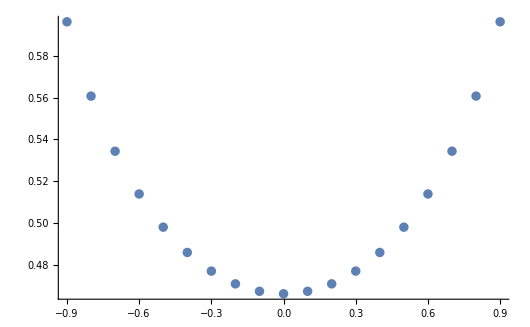

```mathematica
ListPlot[Tqrect ]
```

```mathematica
ExpSecMomZdeborovaLimit[q0_,K_]:=NIntegrate[(ⅇ^(-z^2/2))/(√(2π))(1/2 Erfc[(-√q0 z-K)/(√2 √(1-q0))]-1/2 Erfc[(-√q0 z+K)/(√2 √(1-q0))])^2,{z,-∞,∞}]
```

```mathematica
qrectSmart[ β_,K_]:=Integrate[(ⅇ^(-y^2/2))/(√(2π))(1/2 Erfc[(-K+(1-2β)y)/(2 √2 √(β(1-β)))]-1/2 Erfc[(K+(1-2β)y)/(2 √2 √(β(1-β)))]),
					{y,-K,K}]
```

```mathematica
tZdeb=Table[{q0,ExpSecMomZdeborovaLimit[ q0,1]},{q0, 0.1,0.9,0.1}]
```

{{0.1,0.46724},{0.2,0.470812},{0.3,0.476929},{0.4,0.48585},{0.5,0.497972},{0.6,0.513868},{0.7,0.534363},{0.8,0.560765},{0.9,0.59636}}

```mathematica
TqrectSmart =Table[{q0,qrectSmart[(q0+1)/2,1]},{q0, -0.9,0.9,0.1}];
```

NIntegrate::precw: The precision of the argument function ((ⅇ^(-y^2/2) (1/2 Erfc[1.62221 (-1+0.9 y)]-1/2 Erfc[1.62221 (1+0.9 y)]))/(√(2 π))) is less than WorkingPrecision (26.).

NIntegrate::precw: The precision of the argument function ((ⅇ^(-y^2/2) (1/2 Erfc[1.17851 (-1+0.8 y)]-1/2 Erfc[1.17851 (1+0.8 y)]))/(√(2 π))) is less than WorkingPrecision (26.).

NIntegrate::precw: The precision of the argument function ((ⅇ^(-y^2/2) (1/2 Erfc[0.990148 (-1+0.7 y)]-1/2 Erfc[0.990148 (1+0.7 y)]))/(√(2 π))) is less than WorkingPrecision (26.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

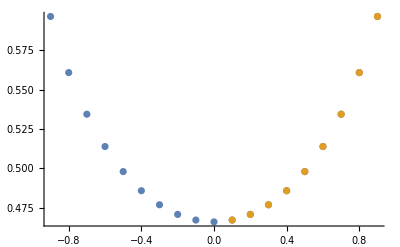

```mathematica
ListPlot[{TqrectSmart,tZdeb}]
```

### Study of Second Moment. Expansion for δq_1 → 0 for Φ_E. Analytic Optimization, y=2, K=1.

```mathematica
Clear["Global`*"]
```

```mathematica
g[z_]:=Exp[-z^2/2]/Sqrt[2π]
H[z_]:=1/2Erfc[z/Sqrt[2]]
```

```mathematica
ΦI[q0_,qh0_,dq1_,qh1_]:=-2qh1-4q0 qh0-2(1-dq1)qh1
```

```mathematica
ΦS[qh0_,qh1_]:=Log[2]+Log[2+4 ⅇ^(2qh1)+ⅇ^(4qh0+4qh1)+ⅇ^(4qh1-4qh0)]
```

```mathematica
P1[z_,q0_,K_]:=1/2 Erfc[(-√q0 z-K)/(√2 √(1-q0))]-1/2 Erfc[(-√q0 z+K)/(√2 √(1-q0))]
```

```mathematica
ExpΦ0E[q0_,k_] := NIntegrate[(ⅇ^(-z^2/2))/(√(2π))(P1[z,q0,k])^2,{z,-∞,∞}]
```

```mathematica
ExpΦE[q0_,dq1_,k_] :=Module[{Int2P1},
Int2P1= ExpΦ0E[q0,k];
Log[Int2P1]+2 NIntegrate[H[z]^2,{z,0,∞}] NIntegrate[(ⅇ^(-z^2/2))/(√(2π))P1[z,q0,k]((ⅇ^(-(k-√q0 z)^2/(2(1-q0))))/(√(2π(1-q0)))+(ⅇ^(-(k+√q0 z)^2/(2(1-q0))))/(√(2π(1-q0)))),{z,-∞,∞}]/Int2P1 √dq1]
```

```mathematica
Φden[q0_, qh0_, dq1_, qh1_,α_,k_]:=ΦI[q0,qh0,dq1,qh1]+ΦS[qh0,qh1]+α ExpΦE[q0,dq1,k]
```

```mathematica
OptΦden[q0_,dq1_,α_,k_]:= Φden[q0,1/4 Log[√((1+q0)/(1-q0))], dq1,1/2 Log[(2 √(1-q0^2))/dq1] ,α,k]
```

```mathematica
OptΦden[0.549,1-0.999,1.8,1.]
```

0.0150501

Very different from true result obtained with Julia and obtained again with Mathematica below avoiding to use the expansion for the energetic part.

```mathematica
t=Table[{q0,OptΦden[q0,0.0001,0.3,1]},{q0,0.1,0.9,0.1 }]
```

{{0.1,1.1546},{0.2,1.14175},{0.3,1.12005},{0.4,1.08901},{0.5,1.04786},{0.6,0.995323},{0.7,0.929324},{0.8,0.846114},{0.9,0.737933}}

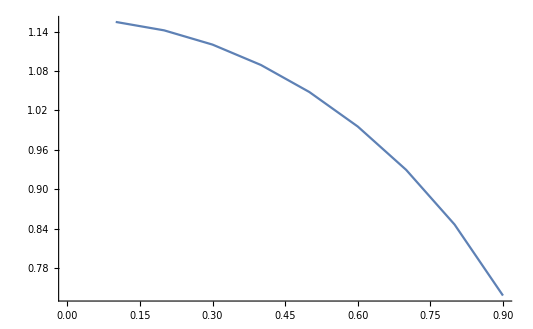

```mathematica
ListPlot[t,Joined->True]
```

```mathematica
Table[{α,q0,OptΦden[q0,0.0001,α,1]},{α,0.1,2,0.1},{q0,0.1,0.9,0.1}];
```

```mathematica
ListPlot[Table[{q0,OptΦden[q0,0.01,α,1]},{α,1.7,2.5,0.1},{q0,0.01,0.99,0.01}],Filling->Axis, Joined->True,AspectRatio->2]
```

```mathematica
Subscript[OptΦ, den][0.9999,0.000001,1.8,1]
```

0.047838

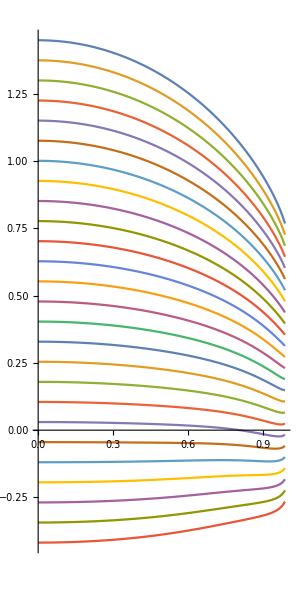

```mathematica
ListPlot[Table[{q0,Subscript[OptΦ, den][q0,0.01,α,1]},{α,0.,2.5,0.1},{q0,0.,1.,0.01}],Filling->Axis, Joined->True,AspectRatio->2,FillingStyle->White]
```

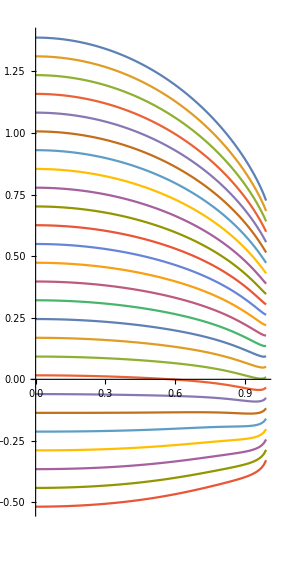

```mathematica
ListPlot[Table[{q0,Subscript[OptΦ, den][q0,0.0001,α,1]},{α,0.,2.5,0.1},{q0,0.,1.,0.01}],Filling->Axis, Joined->True,AspectRatio->2,FillingStyle->White]
```

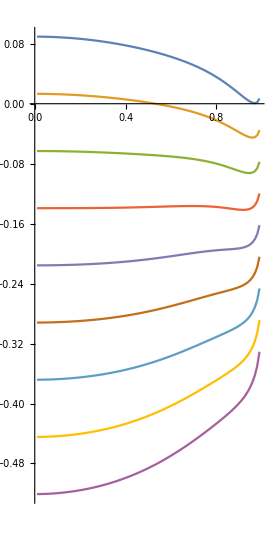

```mathematica
Table[{q0,Subscript[OptΦ, den][q0,0.0,α,1]},{α,1.7,2.5,0.1},{q0,0.01,0.99,0.01}]
```

```mathematica
Table[{α,q0,Subscript[OptΦ, den][q0,0.0001,α,1]},{α,0.1,2,0.1},{q0,0.1,0.9,0.1}];
```

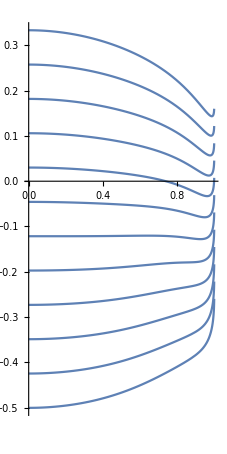

```mathematica
With[{α=Range[1.4,2.5,0.1]},Plot[Subscript[OptΦ, den][q0,0.001,α,1],{q0,0,1},AspectRatio->2]]
```

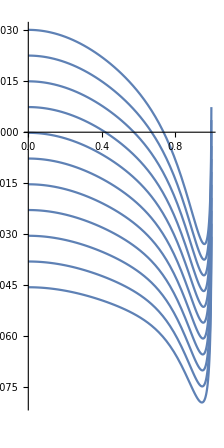

```mathematica
With[{α=Range[1.8,1.9,0.01]},Plot[Subscript[OptΦ, den][q0,0.001,α,1],{q0,0,1},AspectRatio->2]]
```

### Study of Second Moment. Analytic Optimization, y=2, K=1.

```mathematica
Clear["Global`*"]
```

```mathematica
g[z_]:=Exp[-z^2/2]/Sqrt[2π]
H[z_]:=1/2Erfc[z/Sqrt[2]]
```

```mathematica
ΦI[q0_,qh0_,dq1_,qh1_]:=-2qh1-4q0 qh0-2(1-dq1)qh1
```

```mathematica
ΦS[qh0_,qh1_]:=Log[2]+Log[2+4 ⅇ^(2qh1)+ⅇ^(4qh0+4qh1)+ⅇ^(4qh1-4qh0)]
```

```mathematica
ΦE0[q0_,dq1_,K_,z_?NumericQ]:=NIntegrate[g[t](H[-K/(√dq1)+(√q0 z+√(1-dq1-q0)t)/(√dq1)]-H[K/(√dq1)+(√q0 z+√(1-dq1-q0)t)/(√dq1)])^2,{t,-∞,∞}]^2
```

```mathematica
ΦE[q0_,dq1_,K_] := Log[NIntegrate[g[z]ΦE0[q0,dq1,K,z], {z,-∞,∞}]]
```

```mathematica
Φden[q0_, qh0_, dq1_, qh1_,α_,k_]:=ΦI[q0,qh0,dq1,qh1]+ΦS[qh0,qh1]+α ΦE[q0,dq1,k]
```

```mathematica
OptΦden[q0_,dq1_,α_,k_]:= Φden[q0,1/4 Log[√((1+q0)/(1-q0))], dq1,1/2 Log[(2 √(1-q0^2))/dq1] ,α,k]
```

```mathematica
Quiet[OptΦden[0.549,1-0.999,1.8,1.]]
```

-0.0351559

This perfectly matches the results that I obtained with Julia in the program 3.0.

```mathematica
LB[q1_]:= Module[{αOpt},
αOpt=FindRoot[OptΦden[0,1-q1,α,1]- OptΦden[q1,1-q1,α, 1],{α,1.8}];
αOpt⟦1,2⟧	
]
```

```mathematica
tUB=Quiet[Table[{x,alphas[2,1-2x,1]},{x,0.0001,0.001,0.0001}]]
```

{{0.0001,1.79192},{0.0002,1.78334},{0.0003,1.7772},{0.0004,1.7723},{0.0005,1.76818},{0.0006,1.76461},{0.0007,1.76145},{0.0008,1.75862},{0.0009,1.75604},{0.001,1.75368}}

```mathematica
tLB=Table[{x, LB[1-2x]},{x,0.0001,0.001,0.0001}]
```

{{0.0001,1.81083},{0.0002,1.80855},{0.0003,1.80673},{0.0004,1.80514},{0.0005,1.80371},{0.0006,1.80238},{0.0007,1.80114},{0.0008,1.79996},{0.0009,1.79883},{0.001,1.79775}}

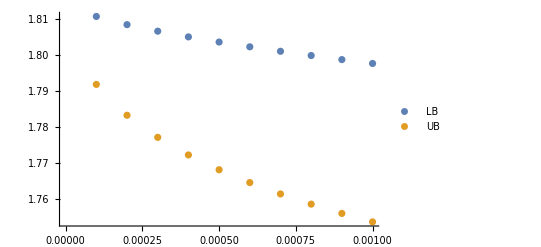

```mathematica
ListPlot[{tLB,tUB}, PlotLegends->{"LB","UB"}]
```

### Study of Second Moment. Numerical Optimization, y=2, K=1.

```mathematica
Clear["Global`*"]
```

```mathematica
g[z_]:=Exp[-z^2/2]/Sqrt[2π]
H[z_]:=1/2Erfc[z/Sqrt[2]]
```

```mathematica
ΦS[qh0_,qh1_]:=Log[2]+Log[2+4 ⅇ^(2qh1)+ⅇ^(4qh0+4qh1)+ⅇ^(4qh1-4qh0)]
```

```mathematica
ΦI[q0_,qh0_,dq1_,qh1_]:=-2qh1-4q0 qh0-2(1-dq1)qh1
```

```mathematica
ΦIS[q0_,qh0_,dq1_,qh1_]:=ΦI[q0,qh0,dq1,qh1]+ΦS[qh0,qh1]
```

```mathematica
OptΦIS[q0_,dq1_]:= Module[{Optima},
Optima=FindRoot [{D[ΦIS[q0,qh0,dq1,qh1],qh0 ]==0,
		D[ΦIS[q0,qh0,dq1,qh1],qh1 ]==0},
		{{qh0,0.1},{qh1,0.2}}];
ΦIS[q0,Optima⟦1,2⟧,dq1,Optima⟦2,2⟧]]
```

```mathematica
ΦE0[q0_,dq1_,K_,z_?NumericQ]:=NIntegrate[g[t](H[-K/(√dq1)+(√q0 z+√(1-dq1-q0)t)/(√dq1)]-H[K/(√dq1)+(√q0 z+√(1-dq1-q0)t)/(√dq1)])^2,{t,-∞,∞}]^2
```

```mathematica
ΦE[q0_,dq1_,K_] := Log[NIntegrate[g[z]ΦE0[q0,dq1,K,z], {z,-∞,∞}]]
```

```mathematica
ΦSM[q0_?NumericQ, dq1_,α_,k_]:=OptΦIS[q0,dq1]+α ΦE[q0,dq1,k]
```

```mathematica
OptΦSM[dq1_,α_,k_]:=FindMaximum[{ΦSM[q0,dq1,α,k],0≤q0< 1-dq1},{q0,0.2}]
```

```mathematica
LB[q1_]:= Module[{αOpt},
αOpt=FindRoot[ΦSM[0,1-q1,α,1]- ΦSM[1,1-q1,α, 1],{α,1.}];
αOpt⟦1,2⟧	
]
```

```mathematica
ΦSM[0.549,1-0.999,1.8,1.]
```

-0.0351561

This results perfectly matches with Julia result, program 3.1.

```mathematica
OptΦSM[0.001,1.2,1.]
```

$Aborted

```mathematica
Quiet[With[{q1=0.999},Table[{q0,ΦSM[q0,1-q1,1.2,1]},{q0,0,q1,0.1}]]]
```

{{0.,0.448232},{0.1,0.446318},{0.2,0.440555},{0.3,0.430871},{0.4,0.417114},{0.5,0.398986},{0.6,0.375896},{0.7,0.346658},{0.8,0.308911},{0.9,0.258719}}

```mathematica
tUB=Quiet[Table[{x,alphas[2,1-2x,1]},{x,0.0001,0.001,0.0001}]]
```

{{0.0001,1.79192},{0.0002,1.78334},{0.0003,1.7772},{0.0004,1.7723},{0.0005,1.76818},{0.0006,1.76461},{0.0007,1.76145},{0.0008,1.75862},{0.0009,1.75604},{0.001,1.75368}}

```mathematica
tLB=Table[{x, LB[1-2x]},{x,0.0001,0.001,0.0001}]
```

{{0.0001,1.81108},{0.0002,1.80904},{0.0003,1.80746},{0.0004,1.80611},{0.0005,1.80491},{0.0006,1.80382},{0.0007,1.8028},{0.0008,1.80185},{0.0009,1.80095},{0.001,1.8001}}

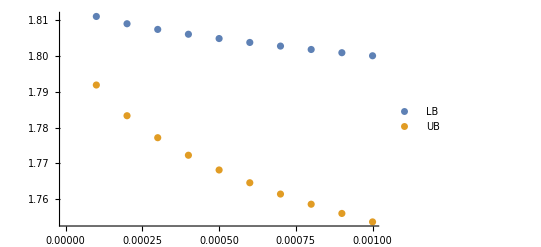

```mathematica
Quiet[ListPlot[{tLB,tUB}, PlotLegends->{"LB","UB"}]]
```

### Study of Second Moment. Numerical Optimization, y=2, K=1. Expansion of Φ_E for δq_1 small.

```mathematica
Clear["Global`*"]
```

```mathematica
g[z_]:=Exp[-z^2/2]/Sqrt[2π]
H[z_]:=1/2Erfc[z/Sqrt[2]]
```

```mathematica
ΦI[q0_,qh0_,dq1_,qh1_]:=-2qh1-4q0 qh0-2(1-dq1)qh1
```

```mathematica
ΦS[qh0_,qh1_]:=Log[2]+Log[2+4 ⅇ^(2qh1)+ⅇ^(4qh0+4qh1)+ⅇ^(4qh1-4qh0)]
```

```mathematica
ΦIS[q0_,qh0_,dq1_,qh1_]:=ΦI[q0,qh0,dq1,qh1]+ΦS[qh0,qh1]
```

```mathematica
OptΦIS[q0_,dq1_]:= Module[{Optima},
Optima=FindRoot [{D[ΦIS[q0,qh0,dq1,qh1],qh0 ]==0,
		D[ΦIS[q0,qh0,dq1,qh1],qh1 ]==0},
		{{qh0,0.1},{qh1,0.2}}];
ΦIS[q0,Optima⟦1,2⟧,dq1,Optima⟦2,2⟧]
]
```

```mathematica
P1[z_,q0_,K_]:=1/2 Erfc[(-√q0 z-K)/(√2 √(1-q0))]-1/2 Erfc[(-√q0 z+K)/(√2 √(1-q0))]
```

```mathematica
ExpΦE0[q0_,k_] := NIntegrate[(ⅇ^(-z^2/2))/(√(2π))(P1[z,q0,k])^2,{z,-∞,∞}]
```

```mathematica
ExpΦE[q0_,dq1_,k_] :=Module[{Int2P1},
Int2P1= ExpΦE0[q0,k];
Log[Int2P1]+2 NIntegrate[H[z]^2,{z,0,∞}] NIntegrate[(ⅇ^(-z^2/2))/(√(2π))P1[z,q0,k]((ⅇ^(-(k-√q0 z)^2/(2(1-q0))))/(√(2π(1-q0)))+(ⅇ^(-(k+√q0 z)^2/(2(1-q0))))/(√(2π(1-q0)))),{z,-∞,∞}]/Int2P1 √dq1]
```

```mathematica
ExpΦSM[q0_?NumericQ, dq1_,α_,k_]:=OptΦIS[q0,dq1]+α ExpΦE[q0,dq1,k]
```

```mathematica
OptΦSM[dq1_,α_,k_]:=FindMaximum[{ExpΦSM[q0,dq1,α,k],0≤q0< 1-dq1},{q0,0.2}]
```

```mathematica
ExpΦSM[0.207,0.001,1.2,1.]
```

0.476429

```mathematica
OptΦSM[0.001,1.2,1.]
```

{0.485065,{q0→0.0011318}}

```mathematica
ΦSM[0.549,1-0.9999,1.8,1.]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-0.0139973

```mathematica
ExpΦSM[0.549,1-0.9999,1.8,1.]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.00183498

```mathematica
With[{dq1=0.001},FindMaximum[{ΦSM[q0,dq1,2.0,1.],0≤q0< 1-dq1},{q0,1-dq1-10^-5}]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-0.120273,{q0→0.641373}}

```mathematica
OptΦSM[0.001,1.2,1.]
```

{0.485065,{q0→0.0011318}}

```mathematica
With[{dq1=0.001},Table[{q0,ΦSM[q0,dq1,2.0,1]},{q0,0,1-dq1,0.001}]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
With[{dq1=0.001},ΦSM[1-dq1,dq1,2.0,1]]
```

-0.0809995

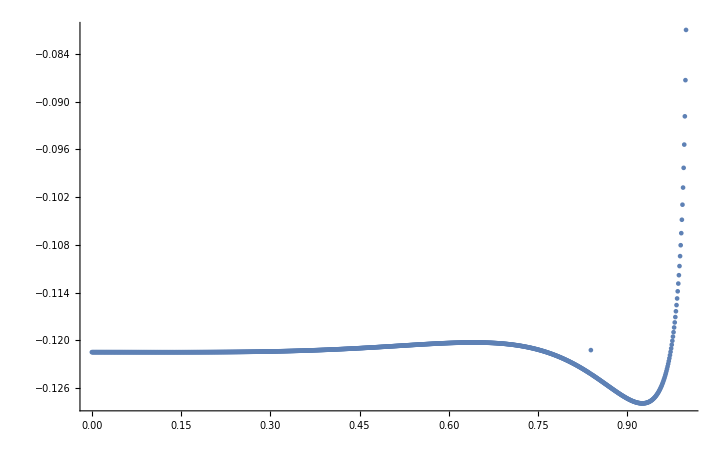

```mathematica
ListPlot[%123, PlotRange->All]
```

```mathematica
LB[q1_]:= Module[{αOpt},
αOpt=FindRoot[ΦSM[0,1-q1,α,1]- ΦSM[q1,1-q1,α, 1],{α,1.8}];
αOpt⟦1,2⟧	
]
```

```mathematica
With[{q1=0.999},Table[{α,ΦSM[0.,1-q1,α,1], ΦSM[q1,1-q1,α, 1]},{α,0.,2.5,0.1}]]
```

{{0.,1.3949,0.702486},{0.1,1.31908,0.663312},{0.2,1.24326,0.624138},{0.3,1.16744,0.584963},{0.4,1.09162,0.545789},{0.5,1.0158,0.506615},{0.6,0.93998,0.46744},{0.7,0.864161,0.428266},{0.8,0.788342,0.389092},{0.9,0.712523,0.349918},{1.,0.636703,0.310743},{1.1,0.560884,0.271569},{1.2,0.485065,0.232395},{1.3,0.409246,0.19322},{1.4,0.333427,0.154046},{1.5,0.257608,0.114872},{1.6,0.181788,0.0756976},{1.7,0.105969,0.0365234},{1.8,0.03015,-0.00265091},{1.9,-0.0456691,-0.0418252},{2.,-0.121488,-0.0809995},{2.1,-0.197307,-0.120174},{2.2,-0.273127,-0.159348},{2.3,-0.348946,-0.198522},{2.4,-0.424765,-0.237697},{2.5,-0.500584,-0.276871}}

```mathematica
tUB=Table[{x,alphas[2,1-2x,1]},{x,0.0,0.001,0.0001}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

```mathematica
tLB=Table[{x, LB[1-2x]},{x,0.,0.001,0.0001}];
```

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {α} = {1.8}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {α} = {1.8}.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

FindRoot::nlnum: The function value {Indeterminate} is not a list of numbers with dimensions {1} at {α} = {1.8}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::inumri: The integrand Indeterminate has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

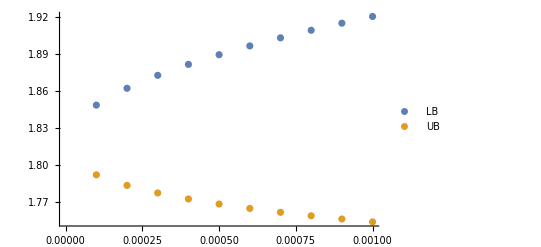

```mathematica
ListPlot[{tLB,tUB}, PlotLegends->{"LB","UB"}]
```

#### Plot of the upper bound and lower bound for K=1 and y=2

```mathematica
alphas[y_,q_,k_]:=-G[y,q]/GEs[y,q, k]
```

```mathematica
phis[y_,q_,α_,k_]:=G[y,q]+α GEs[y,q,k]
```

```mathematica
Subscript[OptΦ1, den][q0_,dq1_,α_,k_]:= Subscript[Φ1, den][q0,1/4 Log[√((1+q0)/(1-q0))], dq1,1/2 Log[(2 √(1-q0^2))/dq1] ,α,k]
```

```mathematica
LB[q1_]:= Module[{αOpt},
αOpt=FindRoot[Subscript[OptΦ1, den][0,1-q1,α,1]- Subscript[OptΦ1, den][q1,1-q1,α, 1],{α,1.8}];
Last[αOpt]	
]
```

```mathematica
LB[0.9999]
```

NIntegrate::inumr: The integrand (ⅇ^(-t^2/2) (1/2 Erfc[(-100.+Times[«2»])/(√2)]-1/2 Erfc[(«19»+«1»)/(√2)])^2)/(√(2 π)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

α→1.81294

```mathematica
With[{q =0.9999},{Last[LB[q]], alphas[2,q,1]}]
```

NIntegrate::inumr: The integrand (ⅇ^(-t^2/2) (1/2 Erfc[(-100.+Times[«2»])/(√2)]-1/2 Erfc[(«19»+«1»)/(√2)])^2)/(√(2 π)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{1.81294,1.79842}

```mathematica
alphas[2,0.998,1]
```

1.75368

```mathematica
Table[{x,alphas[2,1-2x,1]},{x,0.001,0.1,0.001}, WorkingPrecision-> 20]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{0.001,1.75368},{0.002,1.73708},{0.003,1.727},{0.004,1.72005},{0.005,1.71497},{0.006,1.71114},{0.007,1.7082},{0.008,1.70593},{0.009,1.70419},{0.01,1.70285},{0.011,1.70185},{0.012,1.70112},{0.013,1.70062},{0.014,1.70031},{0.015,1.70017},{0.016,1.70016},{0.017,1.70027},{0.018,1.70049},{0.019,1.70079},{0.02,1.70118},{0.021,1.70163},{0.022,1.70214},{0.023,1.7027},{0.024,1.70331},{0.025,1.70396},{0.026,1.70464},{0.027,1.70536},{0.028,1.7061},{0.029,1.70686},{0.03,1.70765},{0.031,1.70846},{0.032,1.70928},{0.033,1.71011},{0.034,1.71095},{0.035,1.71181},{0.036,1.71267},{0.037,1.71354},{0.038,1.71441},{0.039,1.71529},{0.04,1.71618},{0.041,1.71706},{0.042,1.71794},{0.043,1.71883},{0.044,1.71971},{0.045,1.7206},{0.046,1.72148},{0.047,1.72236},{0.048,1.72324},{0.049,1.72411},{0.05,1.72498},{0.051,1.72585},{0.052,1.72671},{0.053,1.72757},{0.054,1.72842},{0.055,1.72927},{0.056,1.73011},{0.057,1.73094},{0.058,1.73177},{0.059,1.73259},{0.06,1.73341},{0.061,1.73422},{0.062,1.73502},{0.063,1.73582},{0.064,1.73661},{0.065,1.73739},{0.066,1.73817},{0.067,1.73894},{0.068,1.7397},{0.069,1.74045},{0.07,1.7412},{0.071,1.74194},{0.072,1.74267},{0.073,1.7434},{0.074,1.74411},{0.075,1.74482},{0.076,1.74553},{0.077,1.74622},{0.078,1.74691},{0.079,1.74759},{0.08,1.74826},{0.081,1.74893},{0.082,1.74959},{0.083,1.75024},{0.084,1.75088},{0.085,1.75152},{0.086,1.75215},{0.087,1.75277},{0.088,1.75339},{0.089,1.754},{0.09,1.7546},{0.091,1.7552},{0.092,1.75579},{0.093,1.75637},{0.094,1.75694},{0.095,1.75751},{0.096,1.75808},{0.097,1.75863},{0.098,1.75918},{0.099,1.75972},{0.1,1.76026}}

```mathematica
Table[{x, Last[LB[1-2x]]},{x,0.001,0.1,0.001}]
```

NIntegrate::inumr: The integrand (ⅇ^(-t^2/2) (1/2 Erfc[(-22.3607+Times[«2»])/(√2)]-1/2 Erfc[(«19»+«1»)/(√2)])^2)/(√(2 π)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.001,1.79775},{0.002,1.78843},{0.003,1.78059},{0.004,1.77353},{0.005,1.76698},{0.006,1.7608},{0.007,1.7549},{0.008,1.74923},{0.009,1.74375},{0.01,1.73844},{0.011,1.73327},{0.012,1.72822},{0.013,1.72329},{0.014,1.71847},{0.015,1.71373},{0.016,1.70908},{0.017,1.70452},{0.018,1.70002},{0.019,1.6956},{0.02,1.69125},{0.021,1.68695},{0.022,1.68272},{0.023,1.67854},{0.024,1.67442},{0.025,1.67035},{0.026,1.66633},{0.027,1.66236},{0.028,1.65844},{0.029,1.65456},{0.03,1.65073},{0.031,1.64693},{0.032,1.64319},{0.033,1.63948},{0.034,1.63581},{0.035,1.63218},{0.036,1.62859},{0.037,1.62503},{0.038,1.62151},{0.039,1.61803},{0.04,1.61458},{0.041,1.61117},{0.042,1.60779},{0.043,1.60445},{0.044,1.60114},{0.045,1.59786},{0.046,1.59462},{0.047,1.5914},{0.048,1.58822},{0.049,1.58507},{0.05,1.58195},{0.051,1.57887},{0.052,1.57581},{0.053,1.57278},{0.054,1.56978},{0.055,1.56682},{0.056,1.56388},{0.057,1.56097},{0.058,1.55809},{0.059,1.55524},{0.06,1.55241},{0.061,1.54962},{0.062,1.54685},{0.063,1.54411},{0.064,1.54139},{0.065,1.53871},{0.066,1.53605},{0.067,1.53342},{0.068,1.53081},{0.069,1.52823},{0.07,1.52568},{0.071,1.52315},{0.072,1.52065},{0.073,1.51817},{0.074,1.51571},{0.075,1.51329},{0.076,1.51088},{0.077,1.5085},{0.078,1.50615},{0.079,1.50381},{0.08,1.5015},{0.081,1.49922},{0.082,1.49696},{0.083,1.49472},{0.084,1.4925},{0.085,1.4903},{0.086,1.48813},{0.087,1.48597},{0.088,1.48384},{0.089,1.48173},{0.09,1.47964},{0.091,1.47757},{0.092,1.47553},{0.093,1.4735},{0.094,1.47149},{0.095,1.4695},{0.096,1.46753},{0.097,1.46558},{0.098,1.46365},{0.099,1.46173},{0.1,1.45984}}

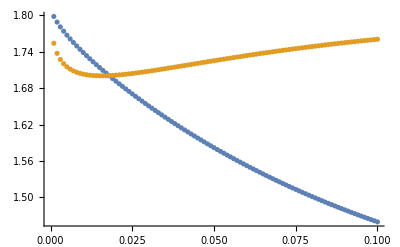

```mathematica
ListPlot[{%45,%33}]
```

This may not work because the expression we use here for OptΦ1_den is valid just for very small δq_1 and for q_0=q_1 the true function and the aprroximated functions are different.

```mathematica
Table[{x,alphas[2,1-2x,1]},{x,0.00001,0.001,0.00001}]
```

{{0.00001,1.80597},{0.00002,1.80452},{0.00003,1.80212},{0.00004,1.80014},{0.00005,1.79842},{0.00006,1.79689},{0.00007,1.7955},{0.00008,1.79422},{0.00009,1.79304},{0.0001,1.79192},{0.00011,1.79088},{0.00012,1.78988},{0.00013,1.78894},{0.00014,1.78804},{0.00015,1.78718},{0.00016,1.78636},{0.00017,1.78556},{0.00018,1.7848},{0.00019,1.78406},{0.0002,1.78334},{0.00021,1.78265},{0.00022,1.78198},{0.00023,1.78132},{0.00024,1.78069},{0.00025,1.78007},{0.00026,1.77947},{0.00027,1.77888},{0.00028,1.77831},{0.00029,1.77775},{0.0003,1.7772},{0.00031,1.77667},{0.00032,1.77614},{0.00033,1.77563},{0.00034,1.77513},{0.00035,1.77463},{0.00036,1.77415},{0.00037,1.77367},{0.00038,1.77321},{0.00039,1.77275},{0.0004,1.7723},{0.00041,1.77186},{0.00042,1.77142},{0.00043,1.771},{0.00044,1.77058},{0.00045,1.77016},{0.00046,1.76975},{0.00047,1.76935},{0.00048,1.76896},{0.00049,1.76857},{0.0005,1.76818},{0.00051,1.7678},{0.00052,1.76743},{0.00053,1.76706},{0.00054,1.7667},{0.00055,1.76634},{0.00056,1.76599},{0.00057,1.76564},{0.00058,1.76529},{0.00059,1.76495},{0.0006,1.76461},{0.00061,1.76428},{0.00062,1.76395},{0.00063,1.76363},{0.00064,1.76331},{0.00065,1.76299},{0.00066,1.76268},{0.00067,1.76236},{0.00068,1.76206},{0.00069,1.76175},{0.0007,1.76145},{0.00071,1.76116},{0.00072,1.76086},{0.00073,1.76057},{0.00074,1.76028},{0.00075,1.76},{0.00076,1.75972},{0.00077,1.75944},{0.00078,1.75916},{0.00079,1.75889},{0.0008,1.75862},{0.00081,1.75835},{0.00082,1.75808},{0.00083,1.75782},{0.00084,1.75756},{0.00085,1.7573},{0.00086,1.75704},{0.00087,1.75679},{0.00088,1.75654},{0.00089,1.75629},{0.0009,1.75604},{0.00091,1.75579},{0.00092,1.75555},{0.00093,1.75531},{0.00094,1.75507},{0.00095,1.75483},{0.00096,1.7546},{0.00097,1.75436},{0.00098,1.75413},{0.00099,1.7539},{0.001,1.75368}}

```mathematica
Table[{x, Last[LB[1-2x]]},{x,0.00001,0.001,0.00001}]
```

NIntegrate::inumr: The integrand (ⅇ^(-t^2/2) (1/2 Erfc[(-223.607+Times[«2»])/(√2)]-1/2 Erfc[(«19»+«1»)/(√2)])^2)/(√(2 π)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{{0.00001,1.81107},{0.00002,1.81405},{0.00003,1.81363},{0.00004,1.81326},{0.00005,1.81294},{0.00006,1.81264},{0.00007,1.8117},{0.00008,1.81139},{0.00009,1.8111},{0.0001,1.81083},{0.00011,1.81057},{0.00012,1.81031},{0.00013,1.81007},{0.00014,1.80984},{0.00015,1.80961},{0.00016,1.80939},{0.00017,1.80917},{0.00018,1.80896},{0.00019,1.80875},{0.0002,1.80855},{0.00021,1.80836},{0.00022,1.80816},{0.00023,1.80797},{0.00024,1.80779},{0.00025,1.8076},{0.00026,1.80742},{0.00027,1.80725},{0.00028,1.80707},{0.00029,1.8069},{0.0003,1.80673},{0.00031,1.80656},{0.00032,1.8064},{0.00033,1.80623},{0.00034,1.80607},{0.00035,1.80591},{0.00036,1.80576},{0.00037,1.8056},{0.00038,1.80545},{0.00039,1.8053},{0.0004,1.80514},{0.00041,1.805},{0.00042,1.80485},{0.00043,1.8047},{0.00044,1.80456},{0.00045,1.80441},{0.00046,1.80427},{0.00047,1.80413},{0.00048,1.80399},{0.00049,1.80385},{0.0005,1.80371},{0.00051,1.80357},{0.00052,1.80344},{0.00053,1.8033},{0.00054,1.80317},{0.00055,1.80304},{0.00056,1.8029},{0.00057,1.80277},{0.00058,1.80264},{0.00059,1.80251},{0.0006,1.80238},{0.00061,1.80226},{0.00062,1.80213},{0.00063,1.802},{0.00064,1.80188},{0.00065,1.80175},{0.00066,1.80163},{0.00067,1.80151},{0.00068,1.80138},{0.00069,1.80126},{0.0007,1.80114},{0.00071,1.80102},{0.00072,1.8009},{0.00073,1.80078},{0.00074,1.80066},{0.00075,1.80054},{0.00076,1.80042},{0.00077,1.80031},{0.00078,1.80019},{0.00079,1.80008},{0.0008,1.79996},{0.00081,1.79984},{0.00082,1.79973},{0.00083,1.79962},{0.00084,1.7995},{0.00085,1.79939},{0.00086,1.79928},{0.00087,1.79917},{0.00088,1.79905},{0.00089,1.79894},{0.0009,1.79883},{0.00091,1.79872},{0.00092,1.79861},{0.00093,1.7985},{0.00094,1.79839},{0.00095,1.79829},{0.00096,1.79818},{0.00097,1.79807},{0.00098,1.79796},{0.00099,1.79786},{0.001,1.79775}}

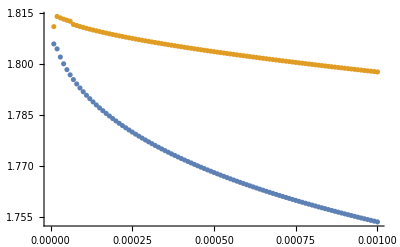

```mathematica
ListPlot[{%50,%51}]
```

```mathematica
Plot[{alphas[2,1-2x,1], LB[1-2x]},{x,0,0.1}, PlotLegends->{"UB","LB"}]
```

$Aborted

NIntegrate::inumr: The integrand (ⅇ^(-t^2/2) (1/2 Erfc[(-31.6228+Times[«2»])/(√2)]-1/2 Erfc[(«19»+«1»)/(√2)])^2)/(√(2 π)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

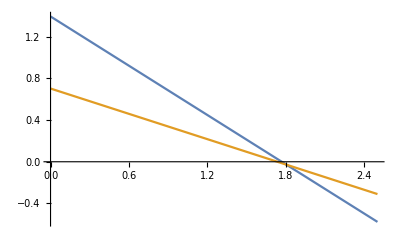

```mathematica
With[{q1=0.999},Plot[{Subscript[OptΦ1, den][0,1-q1,α,1], Subscript[OptΦ1, den][q1,1-q1,α, 1]},{α,0,2.5}]]
```

```mathematica
algh[y_]:=Last[FindRoot[x^2+ 3 y,{x,0.2}]]
```

```mathematica
algh[-5]
```

x→3.87298

```mathematica
Last[algh[-5]]
```

3.87298